### Problem (1)

#### Part (a)

```mathematica
q1aiii=RootLocusPlot[TransferFunctionModel[{{1/((s+c)^3+4s+1)}},s],{c,0,50}];
Export["\\\\wsl.localhost\\Ubuntu\\home\\xueqilin\\engsci-2t4\\aer372\\psets\\A3_imgs\\q1aiii.png",q1aiii]
```

\\wsl.localhost\Ubuntu\home\xueqilin\engsci-2t4\aer372\psets\A3_imgs\q1aiii.png

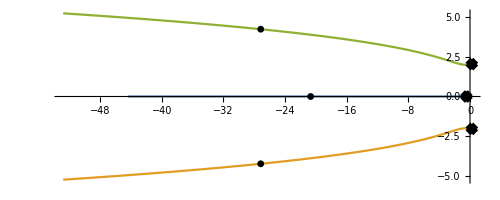

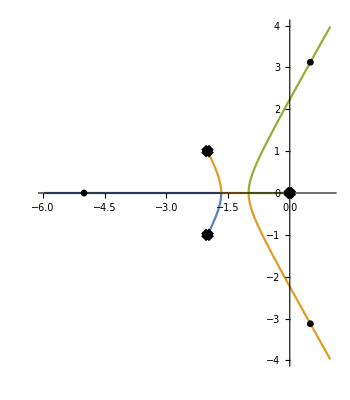

```mathematica
RootLocusPlot[TransferFunctionModel[K*1/(s(s^2+4s+5)),s],{K,0,100}]
```

### Problem (3)

{{s→Root-3.02Root[96+216 #1+211 #1^2+104 #1^3+18 #1^4&,1]-3.015795337700959},{s→Root-1.15Root[96+216 #1+211 #1^2+104 #1^3+18 #1^4&,2]-1.1487759142427278},{s→Root-0.807-0.943 ⅈRoot[96+216 #1+211 #1^2+104 #1^3+18 #1^4&,3]-0.8066032629170455},{s→Root-0.807+0.943 ⅈRoot[96+216 #1+211 #1^2+104 #1^3+18 #1^4&,4]-0.8066032629170455}}

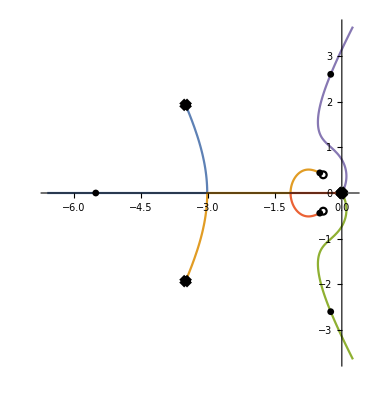

```mathematica
Solve[D[(s^2+(5/6)s+(1/3))/(s^3(s^2+(6+1)s+(16+0))),s]==0]
RootLocusPlot[TransferFunctionModel[K*(s^2+(5/6)s+(1/3))/(s^3(s^2+(6+1)s+(16+0))),s],{K,0,100}]
```

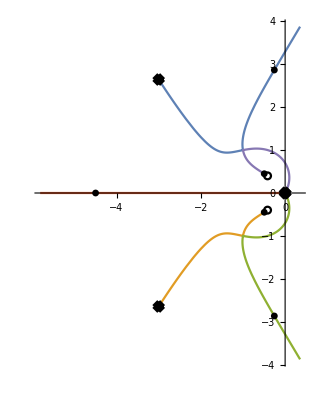

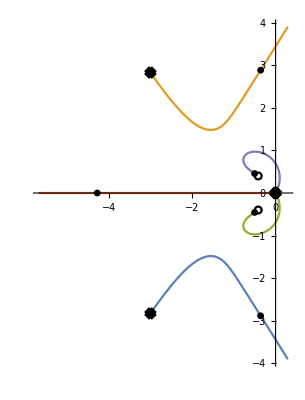

-Graphics-

```mathematica
q3a=RootLocusPlot[TransferFunctionModel[K*(s^2+(5/6)s+(1/3))/(s^3(s^2+(6+0)s+(16+0))),s],{K,0,100}]
q3b=RootLocusPlot[TransferFunctionModel[K*(s^2+(5/6)s+(1/3))/(s^3(s^2+(6+0)s+(16+1))),s],{K,0,100}]
q3c=RootLocusPlot[TransferFunctionModel[K*(s^2+(5/6)s+(1/3))/(s^3(s^2+(6+1)s+(16+0))),s],{K,0,100}]
Export["\\\\wsl.localhost\\Ubuntu\\home\\xueqilin\\engsci-2t4\\aer372\\psets\\A3_imgs\\q3a.png",q3a];
Export["\\\\wsl.localhost\\Ubuntu\\home\\xueqilin\\engsci-2t4\\aer372\\psets\\A3_imgs\\q3b.png",q3b];
Export["\\\\wsl.localhost\\Ubuntu\\home\\xueqilin\\engsci-2t4\\aer372\\psets\\A3_imgs\\q3c.png",q3c];
```

```mathematica
Solve[s^3(s^2+(6+0)s+(16+0))==0,s]
Solve[s^3(s^2+(6+0)s+(16+1))==0,s]
Solve[s^3(s^2+(6+1)s+(16+0))==0,s]
```

{{s→0},{s→0},{s→0},{s→-3-ⅈ √7},{s→-3+ⅈ √7}}

{{s→0},{s→0},{s→0},{s→-3-2 ⅈ √2},{s→-3+2 ⅈ √2}}

{{s→0},{s→0},{s→0},{s→1/2 (-7-ⅈ √15)},{s→1/2 (-7+ⅈ √15)}}

```mathematica
Solve[s^2+(5/6)s+(1/3)==0,s]
```

{{s→1/12 (-5-ⅈ √23)},{s→1/12 (-5+ⅈ √23)}}

```mathematica
Solve[D[s^3(s^2+(6+0)s+(16+0))+s^2+(5/6)s+(1/3),s]==0,s]
```

{{s→Root-2.38-1.93 ⅈRoot[5+12 #1+288 #1^2+144 #1^3+30 #1^4&,1]-2.383248258735836},{s→Root-2.38+1.93 ⅈRoot[5+12 #1+288 #1^2+144 #1^3+30 #1^4&,2]-2.383248258735836},{s→Root-0.0168-0.132 ⅈRoot[5+12 #1+288 #1^2+144 #1^3+30 #1^4&,3]-0.016751741264164264},{s→Root-0.0168+0.132 ⅈRoot[5+12 #1+288 #1^2+144 #1^3+30 #1^4&,4]-0.016751741264164264}}

```mathematica
Solve[D[s^3(s^2+(6+0)s+(16+1))+s^2+(5/6)s+(1/3),s]==0,s]
```

{{s→Root-2.38-2.09 ⅈRoot[5+12 #1+306 #1^2+144 #1^3+30 #1^4&,1]-2.3840105286482762},{s→Root-2.38+2.09 ⅈRoot[5+12 #1+306 #1^2+144 #1^3+30 #1^4&,2]-2.3840105286482762},{s→Root-0.0160-0.128 ⅈRoot[5+12 #1+306 #1^2+144 #1^3+30 #1^4&,3]-0.01598947135172357},{s→Root-0.0160+0.128 ⅈRoot[5+12 #1+306 #1^2+144 #1^3+30 #1^4&,4]-0.01598947135172357}}

### Problem (4)

```mathematica
G[s_]:=1/((s+1)(s+5))
Dc[s_,K_,a_]:=K*(s+a)/(s+8)
TT[K_,a_]:=TransferFunctionModel[{{G[s]*Dc[s,K,a]}},s]
Manipulate[RootLocusPlot[TT[K,a],{K,0,30},ImageSize->400,AspectRatio->1,PlotStyle->Thick],{a,0,10}]
```

### Problem (5)

```mathematica
q5a=RootLocusPlot[TransferFunctionModel[K/(s^3+5s^2),s],{K,0,100}];
Export["\\\\wsl.localhost\\Ubuntu\\home\\xueqilin\\engsci-2t4\\aer372\\psets\\A3_imgs\\q5a.png",q5a];
```

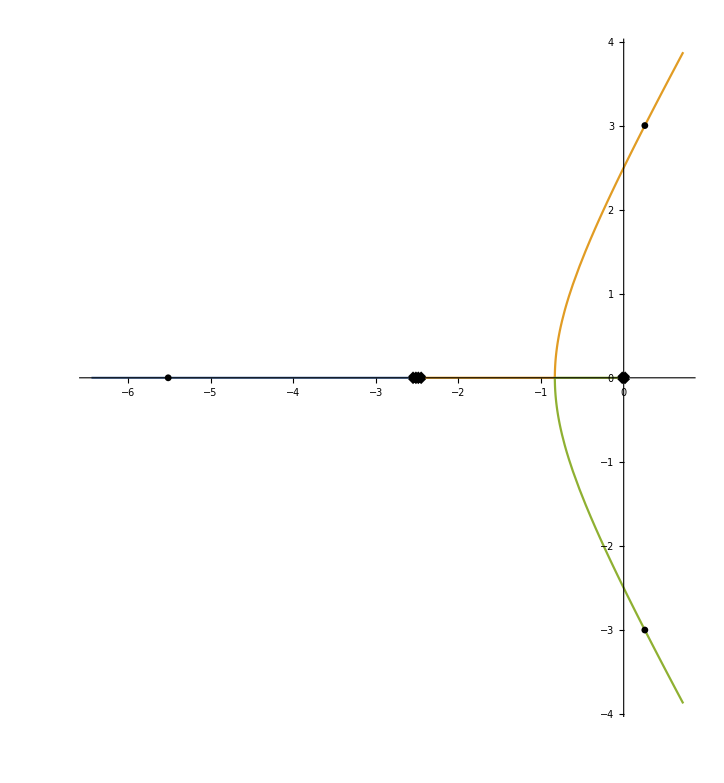

```mathematica
RootLocusPlot[TransferFunctionModel[K/(s(25/4-0.001+s(s+5))),s],{K,0,100}]
K/(s(5+s(s+5)))
```

```mathematica
Manipulate[RootLocusPlot[TransferFunctionModel[K/(s(Kt+s(s+5))),s],{K,0,100}],{Kt,0,10}]
```

```mathematica
DynamicModule[{Kt=0},RootLocusPlot[TransferFunctionModel[K/(s (Kt+s (s+5))),s],{K,0,100}]]
```

### Problem (6)

```mathematica
TT[K_,beta_]:=TransferFunctionModel[(K(1+0.6/s+beta*s))/((s+1)(s+5)),s]
Manipulate[RootLocusPlot[TT[K,beta],{K,0,100},ImageSize->400,AspectRatio->1,PlotStyle->Thick],{beta,0,1}]
```

```mathematica
(□_□)_□
```

### Other Stuff

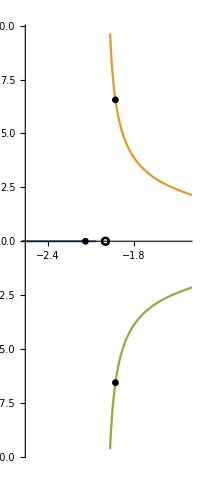

(a K+K s)/(s (1+s) (5+s))

```mathematica
RootLocusPlot[TransferFunctionModel[(K(1+2/s))/((s+1)(s+5)),s],{K,0,100}]
(K(s+a))/(s(s+1)(s+5))//ExpandNumerator
```

```mathematica
G[s_]:=1/((s+1)(s+5))
PID[s_,K_,KI_,KD_]:=K(1+KD*s+KI/s)
TT[K_,KI_,KD_]:=TransferFunctionModel[{{G[s]*PID[s,K,KI,KD]}},s]
Manipulate[RootLocusPlot[TT[K,KD,KI],{K,0,30},ImageSize->400,AspectRatio->1,PlotStyle->Thick],{KD,0,10},{KI,0,1}]
```

```mathematica
OutputResponse[TransferFunctionModel[{{{1}},1+s},s],Sin[10 t],t]
```

{-1/101 ⅇ^-t (-10+10 ⅇ^t Cos[10 t]-ⅇ^t Sin[10 t])}